# Practical - 4

## To solve differential equation using variation of parameter

## Question -1: y’’(x)+ y = sec(x) (Solving without any program)

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

Cos[x]

Sin[x]

1

Log[Cos[x]]

x

Cos[x] Log[Cos[x]]+x Sin[x]

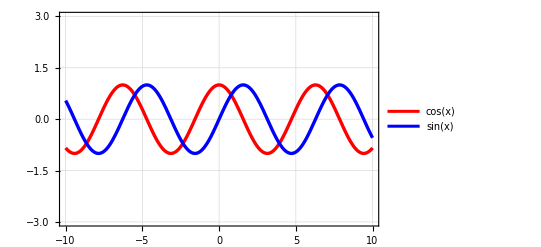

```mathematica
sol=DSolve[y''[x]+y[x] ==0,y[x],x]
y1=y[x]/.sol[[1]]/.{C[1]->1,C[2]->0}
y2=y[x]/.sol[[1]]/.{C[1]->0,C[2]->1}
w=Wronskian[{y1,y2},x]
v1=-Integrate[(y2*Sec[x])/w,x]
v2=Integrate[(y1*Sec[x])/w,x]
pi=Simplify[v1*y1+v2*y2]

Plot[{y1,y2}, {x,-10,10},PlotRange->{-3,3},PlotLegends->{y1,y2},PlotStyle->{{Red,Thickness[0.006]},{Blue,Thickness[0.006]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]
```

## Creating function for 2nd order differential equation

```mathematica
VariationPara[homo_, rhs_, y_, x_] := Block[{sol, y1, y2, w, v1, v2}, 
sol= DSolve[homo, y[x], x];
y1= y[x]/.sol[[1]]/.{C[1]->1,C[2]->0};
y2 = y[x]/.sol[[1]]/.{C[1]->0,C[2]->1};
w = Wronskian[{y1,y2},x];
v1= -Integrate[((y2*rhs)/w),x];
v2= Integrate[((y1*rhs)/w),x];
q1=Simplify[v1*y1 + v2*y2];
Print[q1];
Plot[{y1,y2}, {x,-10,10},PlotRange->{-3,3},PlotLegends->{y1,y2},PlotStyle->{{Blue,Thickness[0.006]},{Red,Thickness[0.006]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]]
```

## Question - 2 : y’’(x)+x^2*y(x)=Cos[x] & y’’[x] +4y’[x]==Sin[2x]*Sex^2[2x]

∫ln[x]ⅆx+ⅇ^-x ∫ln[x]/(-Cosh[x]+Sinh[x])ⅆx

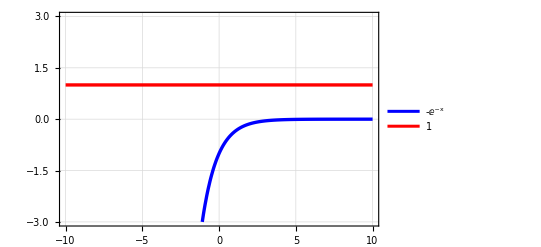

```mathematica
VariationPara[{y''[x]+y'[x]==0}, ln[x], y,x]
```

1/4 (-2 Cos[2 x] ∫Sec^2[2 x] Sin[2 x]^2ⅆx+(∫Sec^2[2 x] Sin[4 x]ⅆx) Sin[2 x])

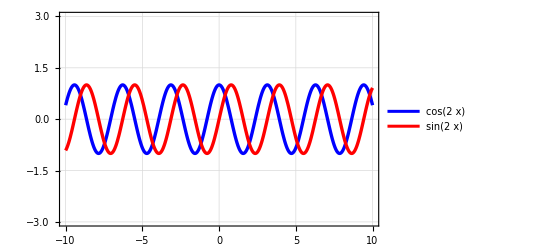

```mathematica
VariationPara[{y''[x]+4*y[x]==0},Sin[2*x]*(Sec^2)[2*x],y,x]
```

## Question -3: y’’[x] -y’[x]-Sin[x]=Sec[x]

1/2 ((∫(Sec[x] (2 ⅇ^x+Cos[x]-Sin[x]))/(Cos[x]-2 ⅇ^x (1+Cos[x])+Sin[x])ⅆx) (2+Cos[x]-Sin[x])-(∫(Sec[x] (2+Cos[x]-Sin[x]))/(Cos[x]-2 ⅇ^x (1+Cos[x])+Sin[x])ⅆx) (2 ⅇ^x+Cos[x]-Sin[x]))

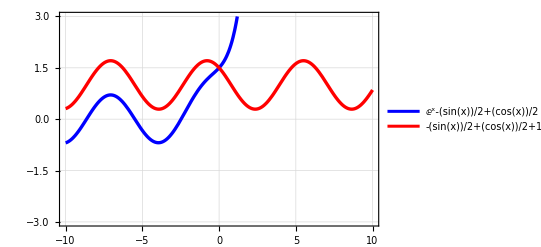

```mathematica
VariationPara[{y''[x]-y'[x]-Sin[x]==0}, Sec[x], y,x]
```

## Creating function for third order differential equation

```mathematica
Variation1Para[homo_, rhs_, y_, x_]:= Block[{sol, y1, y2, y3, w, w1, w2, w3, v1, v2, v3},
sol= DSolve[homo, y[x], x];
y1= y[x]/.sol[[1]]/.{C[1]->1,C[2]->0, C[3]->0};
y2 = y[x]/.sol[[1]]/.{C[1]->0,C[2]->1, C[3]-> 0};
y3 = y[x]/.sol[[1]]/.{C[1]->0,C[2]->0, C[3]-> 1};
w = Wronskian[{y1,y2,y3},x];
w1 = Wronskian[{y2,y3},x];
w2 = Wronskian[{y1,y3},x];
w3 = Wronskian[{y1,y2},x];
v1= Integrate[(w1*rhs)/w,x];
v2= -{Integrate[(w2*rhs)/w,x]};
v3= Integrate[(w3*rhs)/w,x];
q1=Simplify[v1*y1 + v2*y2 + v3*y3];
Print[q1];
Plot[{y1,y2,y3}, {x,-10,10},PlotRange->{-3,3},PlotLegends->{y1,y2,y3},PlotStyle->{{Orange,Thickness[0.006]},{Red,Thickness[0.006]},{Blue,Thickness[0.006]}},Frame->True,GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed]]]
```

## Question 4: y’’’[x] + y’’[x] ==Sin[x]

{1/2 (Cos[x]-Sin[x])}

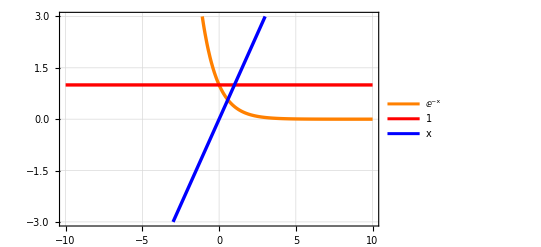

```mathematica
Variation1Para[y'''[x]+y''[x]==0, Sin[x], y, x]
```

## Question 5 : y’’’[x]-y’[x]==0

{1/2 (Cos[x]+Sin[x])}

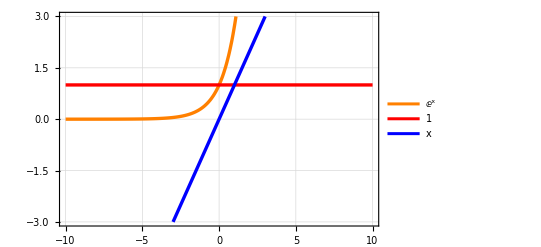

```mathematica
Variation1Para[y'''[x]-y''[x]==0, Sin[x], y, x]
```